```mathematica
<<Toolbox`Style`
<<Toolbox`
```

## Merging models

### Merge the glycolytic, pentose phosphate, nucleotide salvage, hemoglobin pathways

```mathematica
SetDirectory[NotebookDirectory[]];
glycolysis=Import["../../models/SB2/glycolysis.m.gz"];
ppp=Import["../../models/SB2/ppp.m.gz"];
salvage=Import["../../models/SB2/salvage.m.gz"];
hemoglobin=Import["../../models/SB2/Hemoglobin.m.gz"];
```

```mathematica
combi=Union[glycolysis,ppp,salvage,hemoglobin];
combi=deleteReactions[combi,{"EX_g6p_c","EX_f6p_c","EX_gap_c","EX_h_c","EX_h2o_c","EX_r5p_c","vamp","vampin","vatpgen"}];
combi//Dimensions
```

{48,53}

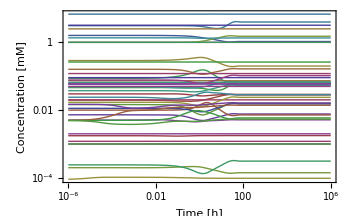

```mathematica
plotSimulation[simulate[combi,{t,0,1000000}][[1]],FrameLabel->{"Time [h]","Concentration [mM]"}]
```

### Relax the model to the new steady-state

```mathematica
combiRelaxed=combi;
updateInitialConditions[combiRelaxed,Flatten[findSteadyState[combi]]]
```

The merged model with the new initial conditions is in a steady-state:

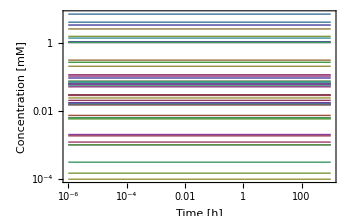

```mathematica
plotSimulation[simulate[combiRelaxed,{t,0,1000}][[1]],FrameLabel->{"Time [h]","Concentration [mM]"}]
```

Comparing the initial conditions of the individual pathways with the newly obtained steady state reveals that fluxes and concentration are not dramatically different:

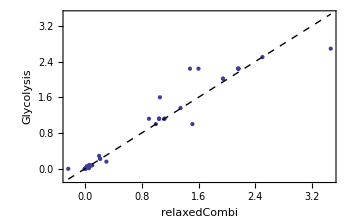

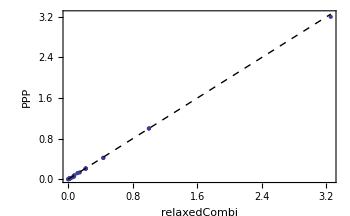

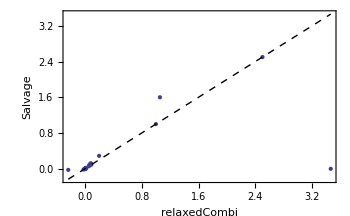

```mathematica
comparisonPlot=Show[ListPlot[Thread[Tooltip[#[[All,2]],#[[All,1]]]],##2],Graphics[{Dashed,Line[{{Min[#[[All,2]]],Min[#[[All,2]]]},{Max[#[[All,2]]],Max[#[[All,2]]]}}]}],PlotRange->Automatic]&;
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],glycolysis["InitialConditions"]]],FrameLabel->{"relaxedCombi","Glycolysis"}]
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],ppp["InitialConditions"]]],FrameLabel->{"relaxedCombi","PPP"}]
comparisonPlot[stripUnits[scatterFromDicts[combiRelaxed["InitialConditions"],salvage["InitialConditions"]]],FrameLabel->{"relaxedCombi","Salvage"}]
```

Simulate the model and reproduce Figure 13.5

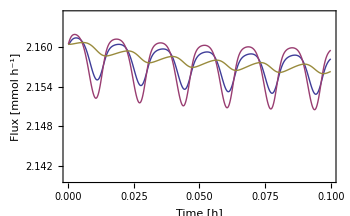

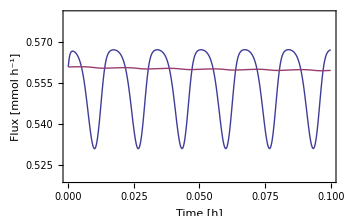

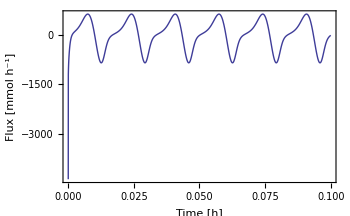

```mathematica
{concSol,fluxSol}=simulate[combiRelaxed,{t,0,.1},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4}];
plotSimulation[FilterRules[fluxSol,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,PlotRange->{All,{2.14,2.165}},Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
plotSimulation[FilterRules[fluxSol,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,PlotRange->{All,{0.52,0.58}},Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
plotSimulation[filter[fluxSol,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
```

### Adjust the model to be close to the book

We have to determine a steady-state flux distribution that is close to the book. The right nullspace has 9 dimensions:

```mathematica
Dimensions[NullSpace[combi]]
```

{9,53}

So, we can fix 9 fluxes to calculate the overall steady-state flux distribution

```mathematica
knownFluxes={Subscript[v, vgluin]==1.12,Subscript[v, vdpgase]==0.441,Subscript[v, vtpi]==1.05,Subscript[v, vprppsyn]==0.014,Subscript[v, vtkii]==0.067,Subscript[v, vino]==0.01,Subscript[v, vpyr]==0.224,Subscript[v, vimpase]==0.014,Subscript[v, vatp]==2.24}
Length[%]
```

{v_vgluin==1.12,v_vdpgase==0.441,v_vtpi==1.05,v_vprppsyn==0.014,v_vtkii==0.067,v_vino==0.01,v_vpyr==0.224,v_vimpase==0.014,v_vatp==2.24}

9

```mathematica
fluxBalances=Thread[0==combi.combi["Fluxes"]];
%//Short
```

{0==-v_vade-v_vadprt,0==-v_vada-v_vado-v_vak+v_vampase,0==v_vak-2 v_vapk+v_vatp+v_vhk+v_vpfk-v_vpgk-v_vpk+2 v_vprppsyn,«42»,0==v_vhbo4,0==v_vgapdh-v_vldh-v_vnadh,0==v_vg6pdh+v_vgl6pdh-v_vgssgr}

```mathematica
newSsFluxes=#[[1]]->#[[2]]Millimole Hour^-1 Liter^-1&/@Solve[Join[fluxBalances,knownFluxes]][[1]];
%//Short
```

{v_vade→-0.014 Millimole Hour^-1 Liter^-1,v_vadprt→0.014 Millimole Hour^-1 Liter^-1,v_vada→0.007 Millimole Hour^-1 Liter^-1,«48»,v_vtkii→0.067 Millimole Hour^-1 Liter^-1,v_vtpi→1.05 Millimole Hour^-1 Liter^-1}

We can include the newly determined fluxes into the initial conditions of the model:

```mathematica
combiCorrect=combi;
updateInitialConditions[combiCorrect,newSsFluxes]
```

We can calculate PERC using the calcPERC funcition. For the reactions that are at a chemical equilibrium we will reuse the rate constant values from the previous model. Unfortunately, a few PERCs are negative,

```mathematica
SortBy[DeleteCases[Quiet@calcPERC[combiCorrect],r_Rule/;!MatchQ[stripUnits[r[[2]]],_?NumberQ]],Last];
%//Short
```

{k_vtki^⟶→-924.225 Liter Hour^-1 Millimole^-1,k_vak^⟶→-283.858 Liter Hour^-1 Millimole^-1,«40»,k_vnh3^⟶→210000. Hour^-1,k_vpgk^⟶→981301. Liter Hour^-1 Millimole^-1}

so, we will change a few equilibrium constants to make them positive:

```mathematica
updateParameters[combiCorrect,{Keq["vtki"]->3,Keq["vampase"]->0.0001 Millimole Liter^-1,Keq["vak"]->1/1000000}]
```

Now, the PERCs are all positive:

```mathematica
newPERCs=SortBy[DeleteCases[Quiet@calcPERC[combiCorrect],r_Rule/;!MatchQ[stripUnits[r[[2]]],_?NumberQ]],Last];
%//Short
```

{k_vak^⟶→0.000021669 Liter Hour^-1 Millimole^-1,k_vampase^⟶→0.0182193 Hour^-1,«40»,k_vnh3^⟶→210000. Hour^-1,k_vpgk^⟶→981301. Liter Hour^-1 Millimole^-1}

Update the model parameters accordingly:

```mathematica
updateParameters[combiCorrect,newPERCs]
```

Simulate the model and reproduce Figure 13.5. For example, the v_dpgm and v_dpgase fluxes values match the book now.

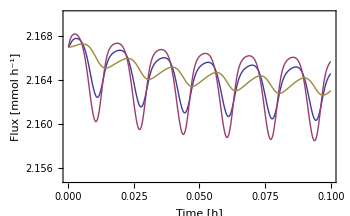

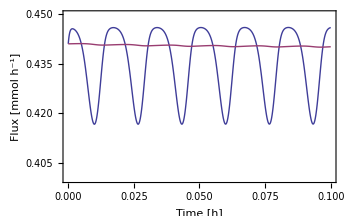

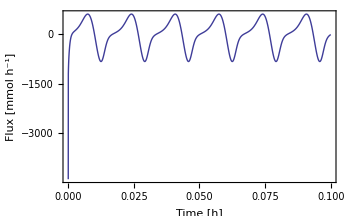

```mathematica
{concSol2,fluxSol2}=simulate[combiCorrect,{t,0,.1},Parameters->{o2^Xt->(70+30 Cos[120 π t])2.8684*10^-4}];
plotSimulation[FilterRules[fluxSol2,{Subscript[v, veno],Subscript[v, vpk],Subscript[v, vpglm]}],PlotFunction->Plot,PlotRange->{All,{2.155,2.17}},Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
plotSimulation[FilterRules[fluxSol2,{Subscript[v, vdpgm],Subscript[v, vdpgase]}],PlotFunction->Plot,PlotRange->{All,{0.4,0.45}},Legend->True,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
plotSimulation[filter[fluxSol2,{Subscript[v, vo2]}],PlotFunction->Plot,FrameLabel->{"Time [h]","Flux [mmol h^-1]"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/RBC.m.gz",combiCorrect]
```

../../models/SB2/RBC.m.gz